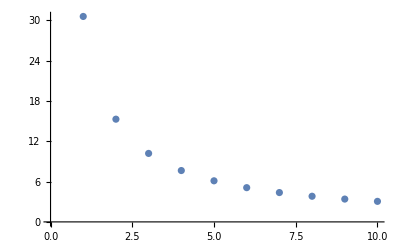

{R→0.0820361}

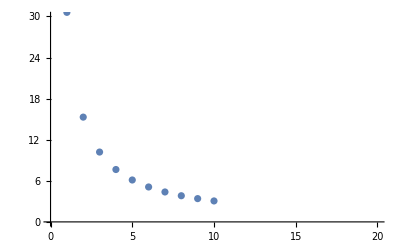

0.00163087

```mathematica
Nexp  = 10;
medidas = {{1.,30.6},{2.,15.3},{3., 10.2}, {4., 7.65}, {5.,6.12},{6, 5.10},{7, 4.37}, {8., 3.82}, {9., 3.40}, {10., 3.06}};
ListPlot[medidas]
modeloP = (373*R)/V;
ajuste1 = FindFit[medidas, modeloP, R, V]
(*FindFit(lista de medidas, modelo, Parametro, Variável*)
(*Retorna o valor do parâmetro*)
(*
Show[
ListPlot[medidas,  PlotRange-> {{0, 20}, {0, 30}}],
Plot[Evaluate[[modeloP/.ajuste1], {V, 0.1, 20}, PlotRange-> {{0, 20}, {0, 30}}]]]
*)
P[V_]:=Evaluate[modeloP/.ajuste1]
Show[ListPlot[medidas, PlotRange-> {{0, 20}, {0, 30}}],Plot[Evaluate[modeloP/ajuste1], {V, 0.1, 20}, PlotRange->{{0, 20}, {0, 30}}]]
rms = Sqrt[(1/Nexp)*Sum[(P[medidas[[i, 1]]]- medidas[[i, 2]])^2, {i, 1, Nexp}]]
```